```mathematica
Integrate[1/(2b*Sqrt[π])Exp[-(x)^2/(4b^2)],{x,c,d}]
```

1/2 (-Erf[c/(2 b)]+Erf[d/(2 b)])

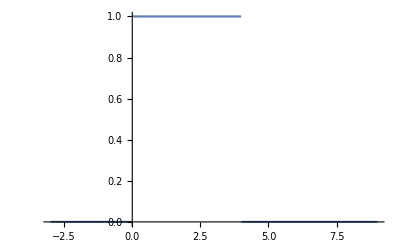

```mathematica
Plot[UnitBox[(x-2)/4],{x,-3,9}]
```

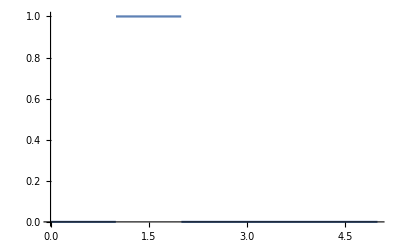

```mathematica
Plot[HeavisideTheta[x-1]-HeavisideTheta[x-2],{x,0,5}]
```

```mathematica
Sqrt[2*π]*FourierTransform[Exp[-σ^2t^2]*Exp[-ⅈ*t*c],t,ω]
```

(ⅇ^(-(c-ω)^2/(4 σ^2)) √π)/(√(σ^2))

```mathematica
Integrate[Cos[ω*τ]*(1/(2*σ*Sqrt[2*π]))*Exp[-ω^2/(2*(2*σ)^2)],{ω,-∞,∞}]
```

ConditionalExpression[(ⅇ^(-2 σ^2 τ^2))/(√(1/σ^2) σ), Re[σ^2]>0]

```mathematica
Integrate[Cos[ω*τ]*(1/(2*σ*Sqrt[2*π]))*Exp[-ω^2/(2*(σ)^2)],{ω,-∞,∞}]
```

ConditionalExpression[(ⅇ^(-1/2 σ^2 τ^2))/(2 √(1/σ^2) σ), Re[σ^2]>0]

```mathematica
test[t_]:=Sum[Cos[2*π*(RandomVariate[NormalDistribution[3,0.5]]*t+RandomReal[{-1,1}])],{i,20}]
```

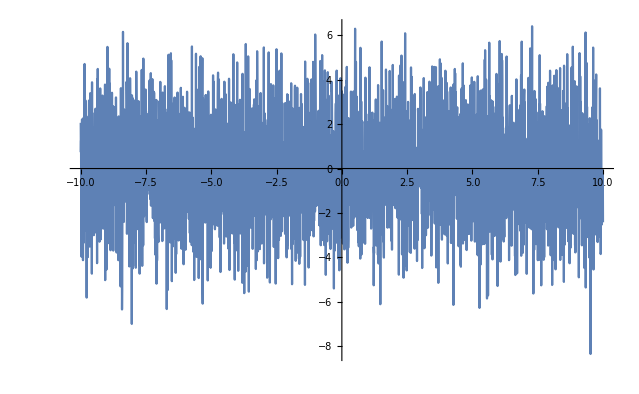

```mathematica
Plot[test[x],{x,-10,10}]
```

```mathematica
test2 = Table[NIntegrate[test[t],{t,0.1*i, 0.1*(i+1)}],{i,0,9}]
```

{-0.411148,-0.0269049,0.358079,-0.0193428,0.268372,0.188742,0.179139,-0.314795,0.141758,0.0299051}

```mathematica
test2x = Table[0.1*(2*i+1)/2,{i,0,9}]
```

{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95}

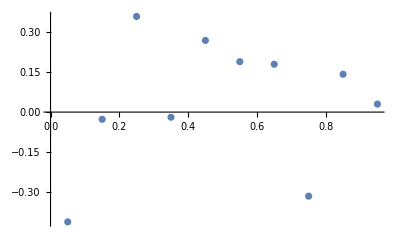

```mathematica
ListPlot[Transpose[{test2x,test2}]]
```

```mathematica
1/(Sqrt[2π]σ)*Integrate[Sin[a*ω]/ω*Exp[-(ω-c)^2/(2σ^2)],{ω,-∞,∞}]
```

(∫_(-∞)^∞ (ⅇ^(-(-c+ω)^2/(2 σ^2)) Sin[a ω])/ω ⅆω)/(√(2 π) σ)